Simple simple system - operator theta is just 4 Sin[b]^2 - so eigenvalues lie between 0 and 4.  I suggest checking this model using the vaccuum set of equations!  If it doesn't work here it doesn't work anywhere!

```mathematica
e=1.5;
Nmax=30;
Clear[psi];
psi=Table[1,{n,1,Nmax+1}];
psi[[2]]=0.25;
psi[[1]]=1;
For[n=3,n≤Nmax+1,n++,psi[[n]]=-psi[[n-2]]+(2-e) psi[[n-1]]];
```

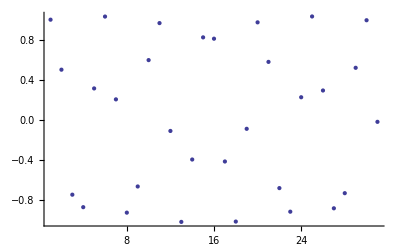

```mathematica
ListPlot[psi]
```

The same system expressed as a vacuum vertex expansion.  I expect it is only meaningful when the sums appearing are convergent or asymptotic.  For example for e=3 - the series below are strongly divergent!  For the positive and negative halves of the amplitude the grow very quickly.  For that reason it appears that even the ratio does not properly describe the expected physical inner product.  It does appear there that the Borel sum gives a result that does satisfy the constraint!!! Holy crap~ one question is how different solutions to the constraitn should appear? Starting w/ different initial states?

```mathematica
Clear[a,b,δ]
Ap[n_]:=2Re[Limit[ⅈ/(2π)Sum[Binomial[2m+n,m] b^(2m+n)/(a+ⅈ δ)^(2m+n+1),{m,0,∞}],δ->0]];
Ap0=2Re[Limit[ⅈ/(2π)Sum[Binomial[2m,m] b^(2m)/(a + ⅈ δ)^(2m+1),{m,0,∞}],δ->0]];
```

```mathematica
Pert=Table[1,{n,1,Nmax+1}];
For[n=0,n≤Nmax,n++,
Clear[a,b];
term=Ap[n]/Ap0;
a=2-e;
b=1;
Pert[[n+1]]=term;]
```

$Aborted

```mathematica
Great! We can see explicitly that the Borel summation of this series does lead to the same expression as solving the constraint equation.  Here we can again make a direct comparison to validate the results of the expansion.  Thus we do see that the series above does provide  an exact expression for the physical inner product when the regulator delta is removed.  Unfortunately we cannot in general carry out the full Borel sum as the series is not so simple. -- and this regulator can be removed only after carrying out the full sum, which is here divergent and has to be analyzed using gneeralizations of summability.  This leads us to wonder how we can extract approximate results at a finite order of the vertex expansion where it is not possible to take the limit delta goes to zero.
```

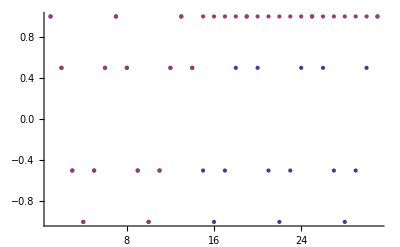

```mathematica
ListPlot[{psi,Pert}]
```

```mathematica
From here we can see that the series is incredibly strongly divergent and clearly does not give good results at a finite point.
```

```mathematica
Clear[a,b];
Aapprox[n_,Mmax_,b_,a_]:=
2Re[ⅈ/(2π)Sum[Binomial[2m+n,m] b^(2m+n)/(a)^(2m+n+1),{m,0,Mmax}]];
singlet[n_,m_,b_,a_]:=2Re[ⅈ/(2π)Binomial[2m+n,m] b^(2m+n)/(a)^(2m+n+1)];
```

```mathematica
a=2-e+ⅈ δ;
δ=0.0001;
b=1;
```

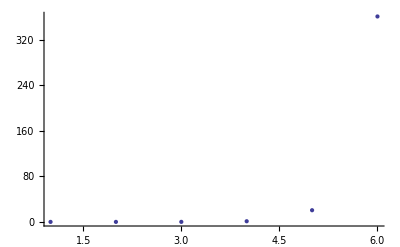

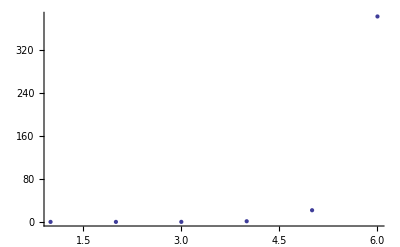

```mathematica
zuh=Table[singlet[0,n,b,a],{n,0,5}];
ListPlot[zuh]
uh=Table[Aapprox[0,n,b,a],{n,0,5}];
ListPlot[uh]
```

```mathematica
Aapprox[1,0,b,a]/Aapprox[0,0,b,a]
```

4.

```mathematica
Under the renormalization flow that we introduced the values a and b flow to their new values abar and bbar
```

```mathematica
abar=(a^2-2 b^2)/a
bbar=b^2/a
```

-3.5+0.0009 ⅈ

2.-0.0004 ⅈ

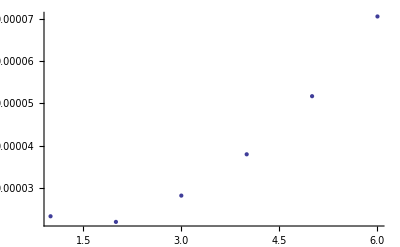

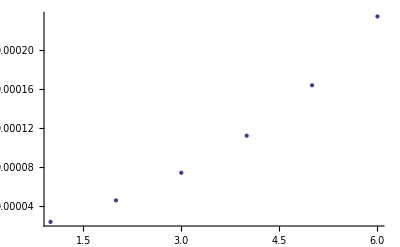

```mathematica
zuh=Table[singlet[0,n,bbar,abar],{n,0,5}];
ListPlot[zuh]
uh=Table[Aapprox[0,n,bbar,abar],{n,0,5}];
ListPlot[uh]
```

```mathematica
Aapprox[3,0,bbar,abar]/Aapprox[0,0,bbar,abar]
```

-0.310982

```mathematica
Comparing the exact value obtained by Borel summation to the approximate values obtained by the first few terms of each expansion for succesive orders of renormalization.
```

```mathematica
Clear[a,b,δ]
a=2-e;
b=1;
Ap0
Ap[1]
```

0.164375

0.0410936

```mathematica
δ=0.0001;
b=1
a=2-e+ⅈ δ
Aapprox[0,0,b,a]
```

1

0.5+0.0001 ⅈ

0.000127324

```mathematica
a1=(a^2-2 b^2)/a;
b1=b^2/a;
a=a1;
b=b1;
Aapprox[0,0,b,a]
```

0.164374

```mathematica
Converges Brilliantly under renormalization!! Approaches a convergent series!!
```